```mathematica
basic=Sum[counts,{b,1,bins}]
```

bins counts

if we ignore the previously binned data and assume that the data is uniform we get a small speedup

```mathematica
basicCmp=Sum[counts-b counts/bins,{b,1,bins}]
```

1/2 (-counts+bins counts)

Doing a binary search can speed things up (list needs to be sorted first)
idx from zero because need to do one sort to get the first bin

```mathematica
sort=counts Log2[counts]+Sum[Log2[counts],{b,0,bins}]
```

((1+bins) Log[counts])/Log[2]+(counts Log[counts])/Log[2]

again assuming uniform scaling we can see what happens if we ignore previously binned data

```mathematica
sortCmp=Sum[Log2[counts-b counts/bins],{b,0,bins}];
Simplify[sortCmp]
```

(2 (1+bins) Log[1/bins]+2 Log[-counts]+2 bins Log[-counts]+Log[1/(2 π)]-2 Zeta^(1,0)[0,-bins])/Log[4]

```mathematica
N[sortCmp/sort/.{bins->10^5,counts->10^2}]
```

Power::indet: Indeterminate expression 0.^0 encountered.

0.782844+0.682188 ⅈ

```mathematica
N[sortCmp/basicCmp/.{bins->10^2,counts->10^6}]
```

0.00003766+9.24785×10^-6 ⅈ

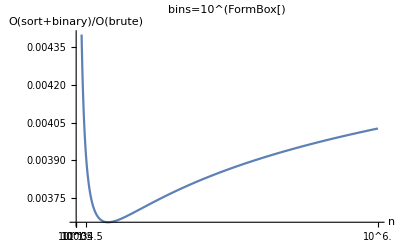

```mathematica
pbins=10^4;
Plot[sort/basicCmp/.{bins->pbins,counts->n},{n,10,10^6},AxesLabel->{"n","O(sort+binary)/O(brute)"},Ticks->{Table[{10^k,Superscript[10,k]},{k,0,6,0.5}],Automatic},PlotLabel->StringForm["bins=10^(``)",Log10[pbins]]]
```

```mathematica
pbins=10^5;
Plot[Abs[sortCmp/basicCmp]/.{bins->pbins,counts->n},{n,10,10^6},AxesLabel->{"n","O(sort+binary)/O(brute)"},Ticks->{Table[{10^k,Superscript[10,k]},{k,0,6,0.5}],Automatic},PlotLabel->StringForm["bins=10^(``)",Log10[pbins]]]
```

Power::indet: Indeterminate expression 0.^0 encountered.

$Aborted

bins=10^(RowBox[{)

```mathematica
Plot3D[sort/basicCmp/.{bins->b,counts->n},{n,10^2,10^6},{b,10^1,10^4},AxesLabel->{"n","b","O(sort+binary)/O(brute)"},PlotLabel->StringForm["bins=10^(``)",Log10[pbins]],PlotPoints->100]
```

-Graphics3D-

```mathematica
Plot3D[Abs[sortCmp/basicCmp]/.{bins->b,counts->n},{n,10^2,10^6},{b,10^1,10^6},AxesLabel->{"n","b","O(sort+binary)/O(brute)"},PlotLabel->StringForm["bins=10^(``)",Log10[pbins]],PlotPoints->10]
```

-Graphics3D-

```mathematica
Plot3D[Abs[sortCmp]/.{bins->b,counts->n},{n,10^2,10^6},{b,10^2,10^6},AxesLabel->{"n","b","O(sort+binary)/O(brute)"},PlotLabel->StringForm["bins=10^(``)",Log10[pbins]],PlotPoints->30]
```

-Graphics3D-